```mathematica
(*read the polygon*)
```

```mathematica
t = Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/polygon/solution/boundary_points_id_6.csv"]
```

{{:0,:1,:2},{0.185714,0.128571,0.},{0.271429,0.157143,0.},{0.357143,0.185714,0.},{0.442857,0.214286,0.},{0.528571,0.242857,0.},{0.614286,0.271429,0.},{0.7,0.3,0.},{0.75,0.35,0.},{0.8,0.4,0.},{0.725,0.425,0.},{0.65,0.45,0.},{0.575,0.475,0.},{0.5,0.5,0.},{0.433333,0.466667,0.},{0.366667,0.433333,0.},{0.3,0.4,0.},{0.25,0.325,0.},{0.2,0.25,0.},{0.15,0.175,0.},{0.1,0.1,0.}}

```mathematica
t = Table[{t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.185714,0.128571},{0.271429,0.157143},{0.357143,0.185714},{0.442857,0.214286},{0.528571,0.242857},{0.614286,0.271429},{0.7,0.3},{0.75,0.35},{0.8,0.4},{0.725,0.425},{0.65,0.45},{0.575,0.475},{0.5,0.5},{0.433333,0.466667},{0.366667,0.433333},{0.3,0.4},{0.25,0.325},{0.2,0.25},{0.15,0.175},{0.1,0.1}}

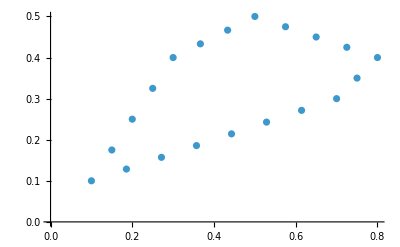

```mathematica
plotpoly=ListPlot[t]
```

```mathematica
(*read the polygon triangulation*)
```

```mathematica
t = Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/polygon/triangles_delaunay.csv"]
```

{{p1:0,p1:1,p2:0,p2:1,p3:0,p3:1},{0.1,0.1,0.7,0.3,0.3,0.4},{0.3,0.4,0.7,0.3,0.5,0.5},{0.5,0.5,0.7,0.3,0.8,0.4}}

```mathematica
t =Table[t[[i]],{i,2,Length[t]}]
```

{{0.1,0.1,0.7,0.3,0.3,0.4},{0.3,0.4,0.7,0.3,0.5,0.5},{0.5,0.5,0.7,0.3,0.8,0.4}}

```mathematica
i=1
```

1

```mathematica
For[plottriangle={};i=1,i<=Length[t],i++,
AppendTo[plottriangle,Graphics[Line[{{t[[i,1]],t[[i,2]]},{t[[i,3]],t[[i,4]]},{t[[i,5]],t[[i,6]]},{t[[i,1]],t[[i,2]]}}]]]
]
```

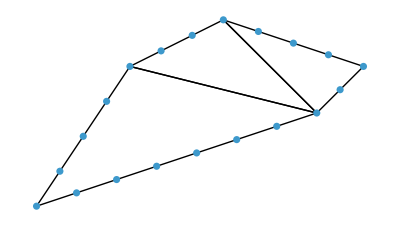

```mathematica
Show[plottriangle,plotpoly]
```